# Release Summary

## v0.8

```mathematica
Import["https://qtechtheory.org/questlink.m"];
CreateDownloadedQuESTEnv[];
```

This release changes the order of the arguments to ApplyCircuit[] (with a warning for old users), adds multi-controlled and multi-target forms of gates R, Rx, Ry, Rz and X (accepted by ApplyCircuit[], DrawCircuit[] and CalcCircuitMatrix[]), and finally adds CalcProbOfAllOutcomes[] and an optimised simulation of the Quantum Fourier Transform, ApplyQFT[].

The below code will use this random density matrix.

```mathematica
n = 5;
ρ = CreateDensityQureg[n];
SetQuregMatrix[ρ, With[{r=Table[RandomComplex[],2^n,2^n]}, r.ConjugateTranspose[r]/Tr[r.ConjugateTranspose[r]]]];
```

## Changes

The order of the arguments to ApplyCircuit[] have changed to accept the input qureg first. This makes it consistent with other functions like ApplyPauliSum[], and furthermore makes cleaner code, since the longer argument (the circuit specification) appears last.

```mathematica
?ApplyCircuit
```

ApplyCircuit[qureg, circuit] modifies qureg by applying the circuit. Returns any measurement outcomes, grouped by M operators and ordered by their order in M.
ApplyCircuit[inQureg, circuit, outQureg] leaves inQureg unchanged, but modifies outQureg to be the result of applying the circuit to inQureg.
Accepts optional arguments WithBackup and ShowProgress.

```mathematica
ApplyCircuit[ρ, Circuit[Subscript[H, 0]]]
```

{}

```mathematica
ApplyCircuit[Circuit[Subscript[X, 0] Subscript[X, 1] Subscript[X, 2]], ρ]
```

ApplyCircuit::error: As of v0.8, the arguments have swapped order for consistency. Please now use ApplyCircuit[qureg, circuit].

$Failed

```mathematica
ApplyCircuit[Circuit[Subscript[X, 0] Subscript[X, 1] Subscript[X, 2]], 0, 1]
```

ApplyCircuit::error: As of v0.8, the arguments have changed order for consistency. Please now use ApplyCircuit[inQureg, circuit, outQureg].

$Failed

Note that CloneQureg still accepts the to-be-modified qureg first, in contrast to ApplyCircuit[]. This cannot be immediately remedied, since the wrong order cannot be detected, and a change would silently break code for previous versions.

```mathematica
?CloneQureg
```

CloneQureg[dest, source] sets dest to be a copy of source.

## New features

Equivalent to QuEST’s calcProbOfAllOutcomes(), one can now compute all probabilities of a given sub-state in one call.

```mathematica
?CalcProbOfAllOutcomes
```

CalcProbOfAllOutcomes[qureg, qubits] returns the probabilities of every classical substate of the given list of qubits. The probabilities are ordered by their corresponding classical value (increasing), assuming qubits is given least to most significant.

```mathematica
CalcProbOfAllOutcomes[ρ, {0,1,2}]
Total[%]
```

{0.116354,0.123616,0.128284,0.132333,0.119562,0.124804,0.132033,0.123013}

1.

All rotation gates now support multiple controls and multiple target qubits.

```mathematica
?Rx
?Ry
?Rz
```

Rx[θ] is a rotation of θ around the x-axis of the Bloch sphere, Exp[-ⅈ θ/2 X ⊗ X ⊗...].

Ry[θ] is a rotation of θ around the y-axis of the Bloch sphere, Exp[-ⅈ θ/2 Y ⊗ Y ⊗...].

Rz[θ] is a rotation of θ around the z-axis of the Bloch sphere, Exp[-ⅈ θ/2 Z ⊗ Z ⊗...].

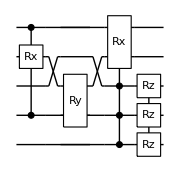

```mathematica
w = Circuit[Subscript[C, 1,4][Subscript[Rx, 3][π]] Subscript[Ry, 1,3][π] Subscript[C, 0,1,2][Subscript[Rx, 3,4][π]] Subscript[Rz, 0,1,2][π] ];
DrawCircuit[w]
ApplyCircuit[ρ,w];
```

This includes Pauli gadgets!

```mathematica
?R
```

R[θ, paulis] is the unitary Exp[-ⅈ θ/2 ⊗ paulis].

```mathematica
u = Circuit[ Subscript[C, 1,2][R[π,Subscript[X, 4] Subscript[Y, 3] Subscript[Z, 0]]] ];
DrawCircuit[u]
ApplyCircuit[ρ, u];
```

-Graphics-

Even the X gate now accepts multiple controls and targets. The multi-target version of X is equivalent to X⊗X⊗X... but is simulated in ApplyCircuit[] significantly move efficiently!

```mathematica
?X
```

X is the Pauli X gate, a.k.a NOT or bit-flip gate.

```mathematica
v = Circuit[ Subscript[X, 0,3,4] Subscript[C, 4,3][Subscript[X, 2,1,0]]];
DrawCircuit[v]
ApplyCircuit[ρ, v];
```

-Graphics-

Equivalent to QuEST’s applyQFT and applyFullQFT, one can efficiently simulate the action of the QFT unitary on a state-vector or density matrix. The implementation is optimised by leveraging the core functions of ApplyPhaseFunc[], and can be monitored using QASM.

```mathematica
?ApplyQFT
```

ApplyQFT[qureg] applies the quantum Fourier transform circuit to the entire register.
ApplyQFT[qureg, qubits] applies the quantum Fourier transform circuit to the given qubits, assuming least-significant first.

```mathematica
StartRecordingQASM[ρ];
ClearRecordedQASM[ρ];
ApplyQFT[ρ,{0,3}];
GetRecordedQASM[ρ]
```

// Beginning of QFT circuit
h q[3];
// Here, applyNamedPhaseFunc() multiplied a complex scalar of form
//     exp(i 1.5707963267949 x y)
//   upon substates informed by qubits (under an unsigned binary encoding)
//     |x> = {0}
//     |y> = {3}
h q[0];
cswap q[0],q[3];
// End of QFT circuit

```mathematica
ClearRecordedQASM[ρ];
ApplyQFT[ρ];
GetRecordedQASM[ρ]
```

// Beginning of QFT circuit
h q[4];
// Here, applyNamedPhaseFunc() multiplied a complex scalar of form
//     exp(i 0.19634954084936 x y)
//   upon substates informed by qubits (under an unsigned binary encoding)
//     |x> = {0, 1, 2, 3}
//     |y> = {4}
h q[3];
// Here, applyNamedPhaseFunc() multiplied a complex scalar of form
//     exp(i 0.39269908169872 x y)
//   upon substates informed by qubits (under an unsigned binary encoding)
//     |x> = {0, 1, 2}
//     |y> = {3}
h q[2];
// Here, applyNamedPhaseFunc() multiplied a complex scalar of form
//     exp(i 0.78539816339745 x y)
//   upon substates informed by qubits (under an unsigned binary encoding)
//     |x> = {0, 1}
//     |y> = {2}
h q[1];
// Here, applyNamedPhaseFunc() multiplied a complex scalar of form
//     exp(i 1.5707963267949 x y)
//   upon substates informed by qubits (under an unsigned binary encoding)
//     |x> = {0}
//     |y> = {1}
h q[0];
cswap q[0],q[4];
cswap q[1],q[3];
// End of QFT circuit